```mathematica
a=0.2;
b=0.1;
```

```mathematica
f[t_]:={0.5+a Cos[t](1-Sin[t]),0.5+ b Sin[t](1+Cos[t])}
```

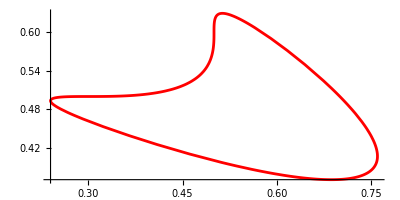

```mathematica
plotcont=ParametricPlot[f[t],{t,0,2π},PlotStyle->Red]
```

```mathematica
g[x_]:=x[[1]]+2x[[2]]
```

```mathematica
Integrate[g[f[t]],{t,0,1}]
```

Integrate::ilim: Invalid integration variable or limit(s) in {{{0.7,0.5},{0.631433,0.560291},{0.566698,0.606331},{0.522451,0.628455},{0.503025,0.624495},{0.5,0.6},{0.496975,0.565716},{0.477549,0.533349},«4»,{0.243091,0.488774},{0.287337,0.466651},{0.379418,0.434284},{0.5,0.4},{0.620582,0.375505},{0.712663,0.371545},{0.756909,0.393669},{0.74899,0.439709}},0,1}.

```mathematica
t=Import["/Users/michelecastellana/Documents/finite_elements/poisson_equation/solve_u/three_domains/check.csv"]
```

{{:0,:1},{0.7,0.5},{0.631433,0.560291},{0.566698,0.606331},{0.522451,0.628455},{0.503025,0.624495},{0.5,0.6},{0.496975,0.565716},{0.477549,0.533349},{0.433302,0.511226},{0.368567,0.501512},{0.3,0.5},{0.25101,0.498488},{0.243091,0.488774},{0.287337,0.466651},{0.379418,0.434284},{0.5,0.4},{0.620582,0.375505},{0.712663,0.371545},{0.756909,0.393669},{0.74899,0.439709}}

```mathematica
t=Table[{t[[i,1]],t[[i,2]]},{i,2,Length[t]}]
```

{{0.7,0.5},{0.631433,0.560291},{0.566698,0.606331},{0.522451,0.628455},{0.503025,0.624495},{0.5,0.6},{0.496975,0.565716},{0.477549,0.533349},{0.433302,0.511226},{0.368567,0.501512},{0.3,0.5},{0.25101,0.498488},{0.243091,0.488774},{0.287337,0.466651},{0.379418,0.434284},{0.5,0.4},{0.620582,0.375505},{0.712663,0.371545},{0.756909,0.393669},{0.74899,0.439709}}

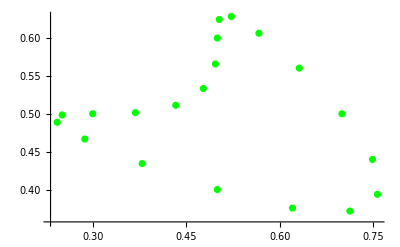

```mathematica
plotdis=ListPlot[t,PlotStyle->Green]
```

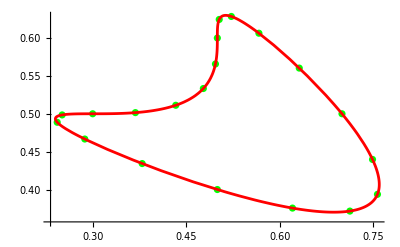

```mathematica
Show[plotdis,plotcont]
```